```mathematica
ClearAll["Global`*"];
(* Znaleźć logarytmiczny dekrement tłumienia Λ wahadła matematycznego o długości l,jeżeli po czasie τ 5min jego całkowita energia drgań zmalała N razy. Sporządzić wykresy zależności Λ od N dla N zmieniającego się od 10 000 do 400 000
w dwóch przypadkach:
l=50 cm     l=100 cm. *)
```

```mathematica
A[t_]=Ao×Exp[-β×t];
```

```mathematica
Λ=Log[A[t]/A[t+T]]
Λ=PowerExpand[Λ]//Simplify
```

Log[ⅇ^(-t β+(t+T) β)]

T β

```mathematica
Ec[t_]=(k×A[t]^2)/2;
```

```mathematica
r=Solve[n==Ec[0]/Ec[τ],β,Reals]
r1=Refine[r,n>0]
β=β/.r1[[1,1]]
```

{{β→ConditionalExpression[Log[n]/(2 τ), n>0]}}

{{β→Log[n]/(2 τ)}}

Log[n]/(2 τ)

```mathematica
ωo=√(g/l)
T=(2×π)/(√(ωo^2-β^2))
```

√(g/l)

(2 π)/(√(g/l-Log[n]^2/(4 τ^2)))

```mathematica
g=9.81;       (* m/s^2 *)
```

```mathematica
τ=300;          (* s *)
```

```mathematica
Λ
```

(π Log[n])/(300 √(9.81/l-Log[n]^2/360000))

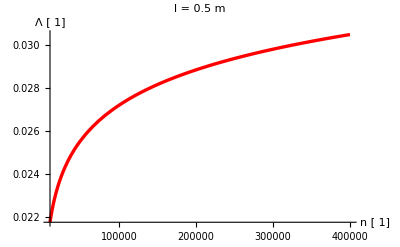

```mathematica
Plot[Λ/.l->0.5,{n,1×10^4,4×10^5},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["l = 0.5 m",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"n [ 1]","Λ [ 1]"}]
```

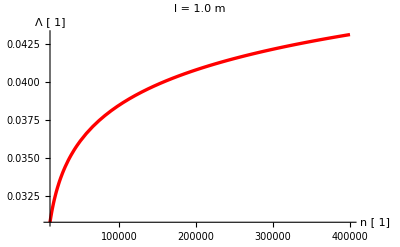

```mathematica
Plot[Λ/.l->1,{n,1×10^4,4×10^5},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},PlotLabel->StyleForm["l = 1.0 m",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"n [ 1]","Λ [ 1]"}]
```

```mathematica
f=10;
β=0.9;
Ao=5;
ϕ=0;
ω=2×π×f
```

20 π

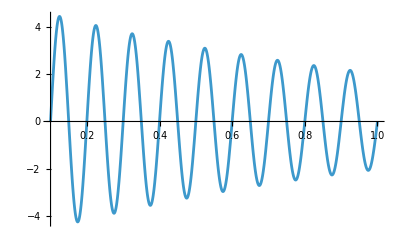

```mathematica
Plot[Ao×Exp[-β×t]×Sin[ω×t+ϕ],{t,0.1,1}]
```